## Segundo Examen Parcial Métodos Numéricos Fernando Ángel Medellín Cuevas A01169814

```mathematica
$PrePrint=TraditionalForm
```

TraditionalForm

#### Problema 1

```mathematica
(*Resolver el sistema de ecuaciones por el método de Gauss-Jordan
−12.377:d835:dc67+11.797:d835:dc64=30
−13.422:d835:dc65+12.252:d835:dc66=300
−12.252:d835:dc66+12.377:d835:dc67=102
13.422:d835:dc65=750.5*)
```

```mathematica
gaussjor[matriz_]:=Module[{mat=matriz},
Table[If[i≠j,mat[[i]]=-mat[[j]]/mat[[j,j]]mat[[i,j]]+mat[[i]]],{j,Length[mat]},{i,Length[mat]}];

Table[mat[[k]]/mat[[k,k]],{k,Length[mat]}]
]
```

```mathematica
(*en la matriz se intercambia el primer renglon con el último ya que si no se hace se indetermina en el primer valor*)
gaussjor[({{13.422, 0, 0, 0, 750.5}, {-13.422, 12.252, 0, 0, 300}, {0, -12.252, 12.377, 0, 102}, {0, 0, -12.377, 11.797, 30}})]
```

(1. | 0. | 0. | 0. | 55.9157
0. | 1. | 0. | 0. | 85.7411
0. | -1.43521×10^-16 | 1. | 0. | 93.1163
0. | -1.50577×10^-16 | 0. | 1. | 100.237)

#### Problema 2

```mathematica
(*Determinante*)
det[matriz_]:=Module[{mat=matriz},
Table[If[i≠j,mat[[i]]=-mat[[j]]/mat[[j,j]]mat[[i,j]]+mat[[i]]],{j,Length[mat]},
{i,Length[mat]}];
 ∏_(g=1)^Length[mat] mat[[g,g]]

]
```

```mathematica
(*para sacar el determinante es necesario hacer intercambio de renglones, para esta matriz es necesario hacer 3 cambios y por cada cambio es hacerle un cambio de signo a cada raiz, es por eso que queda positivo*)
det[({{1, 2, 1, 2, 1}, {1, 1, 0, 0, 0}, {1, 2, 2, 1, 1}, {0, 0, 1, 1, 2}, {0, 0, 1, 1, 1}})]
```

2

#### Problema 3

```mathematica
(*mat1=Drop[mat,0,-1]
mataux=Transpose[mat1]
match=Transpose[Drop[mat,0,3]]
mataux[[i]]=match[[1]]
Det[Transpose[mataux]/det[mat1],{1,Length[mat]}]*)
(*
mat[({{4, 1, -1, 1}, {1, 4, 0, -1}, {-1, -1, 5, 1}, {1, 1, 1, 3}})];
b[({{-2}, {-1}, {0}, {1}})]
mat1=Transpose[mat];
mat1[[1]]=b;
mat2[[2]]=b;
mat3[[3]]=b;
mat4[[4]]=b;
x=Table[0,{i,Dimensions[mat][[1]]}];
x1=Table[0,{i,Dimensions[mat][[2]]}];
x2=Table[0,{i,Dimensions[mat][[3]]}];
x3=Table[0,{i,Dimensions[mat][[4]]}];

x[[1]]=Det[Transpose[mat1]]/Det[mat]
x1[[2]]=Det[Transpose[mat2]]/Det[mat]
x2[[3]]=Det[Transpose[mat3]]/Det[mat]
x3[[4]]=Det[Transpose[mat3]]/Det[mat]

mat2=Transpose[mat];
mat1[[2]]=b;
x=Table[0,{i,Dimensions[mat][[2]]}];
x[[2]]=Det[Transpose[mat1]]/Det[mat]

*)
```

(27
-61.5
-21.5)((-2
-1
0
1))

Set::partw: Part 4 of {{{27},{-61.5},{-21.5}},{{27},{-61.5},{-21.5}},{{27},{-61.5},{-21.5}}} does not exist.

Part::partw: Part 3 of {3,3} does not exist.

Table::iterb: Iterator {i,{3,3}⟦3⟧} does not have appropriate bounds.

Det::matsq: Argument {{{27},{27},{27}},{{-61.5},{-61.5},{-61.5}},{{-21.5},{-21.5},{-21.5}}} at position 1 is not a non-empty square matrix.

-0.00346021 Det[({27} | {27} | {27}
{-61.5} | {-61.5} | {-61.5}
{-21.5} | {-21.5} | {-21.5})]

Det::matsq: Argument {{{27},{27},{27}},{{-61.5},{-61.5},{-61.5}},{{-21.5},{-21.5},{-21.5}}} at position 1 is not a non-empty square matrix.

-0.00346021 Det[({27} | {27} | {27}
{-61.5} | {-61.5} | {-61.5}
{-21.5} | {-21.5} | {-21.5})]

#### Problema 4

```mathematica
gs[mat_,b_,xi_,n_,pre_]:=Module[{lb=Length[b]},{x[1],x[2],x[3]}=SetPrecision[{xi[[1]],xi[[2]],xi[[3]]},pre];
																				               (*## &[]] quita todo los nulls que se generan en el programa*)
Table[x[i]=1/mat[[i,i]](b[[i]]-∑_(j=1)^lb If[i≠j,mat[[i,j]]x[j],##&[]]),{n},{i,lb}];Table[x[k],{k,lb}]
]
```

```mathematica
(*Acomodo por matriz dominante*)
gs[mat=({{10, 2, -1.}, {-3, -6, 2.}, {1, 1, 5.}}),b=({{27}, {-61.5}, {-21.5}}),{0,0,0},5,5]
```

(0.500253
8.00011
-6.00007)

```mathematica
(*Agregar la instrucción fuera de las llaves en la instrucción module ya que va a unir las 2 matrices*)
inversaotra[matri_]:=
Drop[gaussjor[Join[matri,IdentityMatrix[Length[matri]],2]],0,Length[matri]]
```

```mathematica
b=({{27}, {-61.5}, {-21.5}});
inversaotra[({{10, 2, -1.}, {-3, -6, 2.}, {1, 1, 5.}})].b
```

(0.5
8.
-6.)

```mathematica
(*errores dados por la inversa
x1= 0.5
x2=8
x3=-6*)
```

```mathematica
errorx1=Abs[((0.5-0.50025)/0.5) 100]
```

0.05

```mathematica
erroresx2=Abs[((8-8.00011)/8) 100]
```

0.001375

```mathematica
erroresx3=Abs[(((-6) -(-6.00007))/-6) 100]
```

0.00116667

```mathematica
{x[1]= 0., x[2]= 0., x[3]=0.};
mat=({{10, 2, -1.}, {-3, -6, 2.}, {1, 1, 5.}}); b=({{27}, {-61.5}, {-21.5}});
```

```mathematica
Table[
x[1]= 1/mat[[1,1]](b[[1,1]]-mat[[1,2]]x[2]-mat[[1,3]]x[3]);
x[2]=1/mat[[2,2]](b[[2,1]]-mat[[2,1]]x[1]-mat[[2,3]]x[3]);
x[3]= 1/mat[[3,3]](b[[3,1]]-mat[[3,1]]x[1]-mat[[3,2]]x[2]);
{x[1],x[2],x[3]},{5}]
```

(2.7 | 8.9 | -6.62
0.258 | 7.91433 | -5.93447
0.523687 | 8.01 | -6.00674
0.497326 | 7.99909 | -5.99928
0.500253 | 8.00011 | -6.00007)

#### Problema5

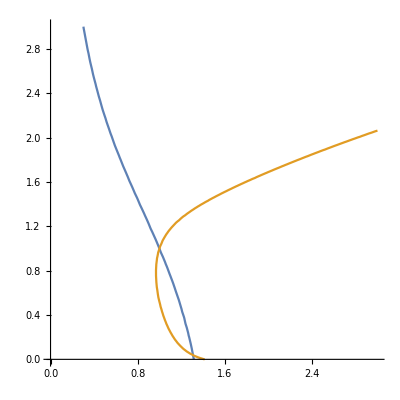

```mathematica
(*graficar para poder encontrar puntos iniciales*)
ContourPlot[{x y^2+x^2 y+x^4-3==0,x^3 y^5-2 x^5 y-x^2+2==0},{x,0,3},{y,0,3},Frame->False,Axes->True]
```

```mathematica
(*definimos las funciones*)
f=({{x y^2+x^2 y+x y^4-3}, {x^3 y^5-2 x^5 y-x^2+2}});x0=({{1}, {1}});
Table[feva= f/.{x->x0[[1,1]],y->x0[[2,1]]};
jac=({{D[f[[1,1]], x], D[f[[1,1]], y]}, {D[f[[2,1]], x], D[f[[2,1]], y]}});
jaceva=jac/.{x->x0[[1,1]],y->x0[[2,1]]};

x0=x0-Inverse[jaceva].feva,{5}];
x0
```

(1
1)